## Kronecker Product

```mathematica
A = {{a,b},{c,d}};
B= {{e,f},{g,h}};
KroneckerProduct[A,B]//MatrixForm
KroneckerProduct[B,A]//MatrixForm
```

(a e | a f | b e | b f
a g | a | b g | b
c e | c f | d e | d f
c g | c | d g | d)

(a e | b e | a f | b f
c e | d e | c f | d f
a g | b g | a | b
c g | d g | c | d)

## TFIM

```mathematica
zz = KroneckerProduct[PauliMatrix[3],PauliMatrix[3]]/4;
tf = KroneckerProduct[PauliMatrix[0],PauliMatrix[1]]/2 + KroneckerProduct[PauliMatrix[1],PauliMatrix[0]]/2;
```

```mathematica
zz//MatrixForm
tf//MatrixForm
```

(1/4 | 0 | 0 | 0
0 | -1/4 | 0 | 0
0 | 0 | -1/4 | 0
0 | 0 | 0 | 1/4)

(0 | 1/2 | 1/2 | 0
1/2 | 0 | 0 | 1/2
1/2 | 0 | 0 | 1/2
0 | 1/2 | 1/2 | 0)

```mathematica
H2=-4 J zz -2 h tf;
H2//MatrixForm
{vals,vecs}=Eigensystem[H2];
```

(-1 | -h | -h | 0
-h | 1 | 0 | -h
-h | 0 | 1 | -h
0 | -h | -h | -1)

```mathematica
Det[H2-λ IdentityMatrix[4]]//FullSimplify
```

-((1+4 h^2-λ^2) (-1+λ^2))

1

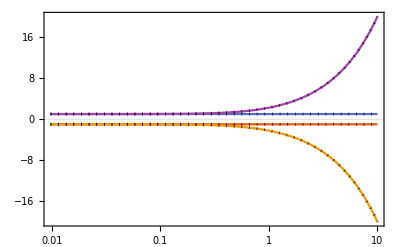

```mathematica
J=1
LogLinearPlot[Evaluate@vals,{h,0,10},PlotTheme->"Scientific",PlotRange->Full];
Show[%,LogLinearPlot[{+1,-1,√(4 h^2+1),-√(4 h^2+1)},{h,0,10},PlotStyle->{{Dotted,Black}},PlotRange->Full]]
```

```mathematica
tf
```

{{0,1/2,1/2,0},{1/2,0,0,1/2},{1/2,0,0,1/2},{0,1/2,1/2,0}}

```mathematica
vecs=(Table[Normalize[v],{v,vecs}]//ComplexExpand//FullSimplify);
```

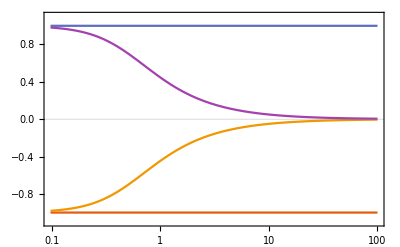

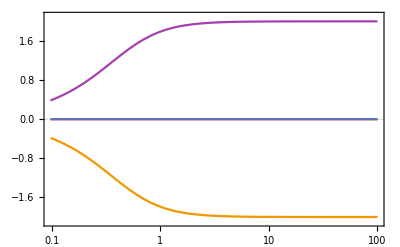

```mathematica
LogLinearPlot[Evaluate@Table[-4vᵀ.zz.v/.h->hh,{v,vecs}],{hh,0,100},PlotRange->1.1{-1,1},PlotTheme->"Scientific"]
LogLinearPlot[Evaluate@Table[-2vᵀ.tf.v/.h->hh,{v,vecs}],{hh,0,100},PlotRange->2.1{-1,1},PlotTheme->"Scientific"]
```

## Heisenberg

```mathematica
xx = KroneckerProduct[PauliMatrix[1],PauliMatrix[1]]/4;
yy = KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]/4;
zz = KroneckerProduct[PauliMatrix[3],PauliMatrix[3]]/4;
tf = KroneckerProduct[PauliMatrix[0],PauliMatrix[1]]/2 + KroneckerProduct[PauliMatrix[1],PauliMatrix[0]]/2;
```

```mathematica
zz//MatrixForm
tf//MatrixForm
```

(1/4 | 0 | 0 | 0
0 | -1/4 | 0 | 0
0 | 0 | -1/4 | 0
0 | 0 | 0 | 1/4)

(0 | 1/2 | 1/2 | 0
1/2 | 0 | 0 | 1/2
1/2 | 0 | 0 | 1/2
0 | 1/2 | 1/2 | 0)

```mathematica
H2=-(4xx+4yy+4zz) -2 h tf;
H2//MatrixForm
{vals,vecs}=Eigensystem[H2];
```

(-1 | -h | -h | 0
-h | 1 | -2 | -h
-h | -2 | 1 | -h
0 | -h | -h | -1)

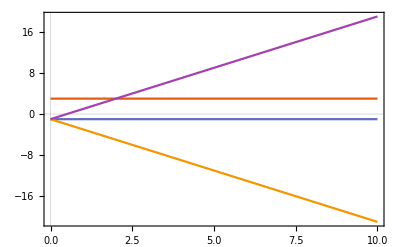

```mathematica
Plot[Evaluate@vals,{h,0,10},PlotTheme->"Scientific"]
```

```mathematica
vecs=(Table[Normalize[v],{v,vecs}]//ComplexExpand//FullSimplify);
```

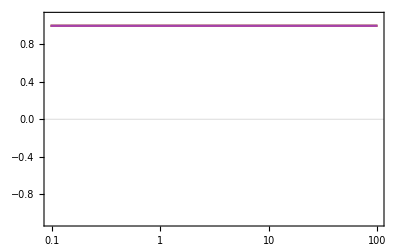

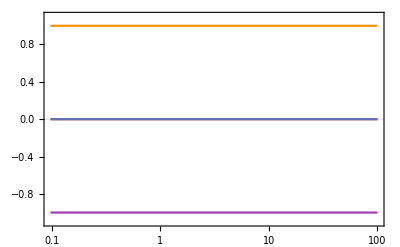

```mathematica
LogLinearPlot[Evaluate@Table[4vᵀ.(xx+yy+zz).v/.h->hh,{v,vecs}],{hh,0,100},PlotRange->1.1{-1,1},PlotTheme->"Scientific"]
LogLinearPlot[Evaluate@Table[vᵀ.tf.v/.h->hh,{v,vecs}],{hh,0,100},PlotRange->1.1{-1,1},PlotTheme->"Scientific"]
```

## Power iteration

```mathematica
Clear[powerIteration,A,b0,n]
powerIteration[A_,b0_,n_:2]:=Module[{b,μ,k,abk,norm},
b[0]=b0;
Do[
abk=A.b[k];
norm=b[k]*.b[k];
μ[k]=b[k]*.abk/norm;
b[k+1]=abk/Norm[abk];

,{k,0,n}];
{b,μ}]
```

```mathematica
Clear[λ,A,B,b,μ,bA,μA,bB,μB,nmax]
λ[1]=1.0;λ[2]=.93;
A={{λ[1],0,0,0},{0,λ[2],0,0},{0,0,λ[2],0},{0,0,0,λ[2]}};
A//MatrixForm
B={{λ[1],0,0,0},{0,λ[2],1,0},{0,0,λ[2],1},{0,0,0,λ[2]}};
B//MatrixForm
{bA,μA}=powerIteration[A,{1,1,1,1},nmax=100000];
{bB,μB}=powerIteration[B,{1,1,1,1},nmax];
```

(1. | 0 | 0 | 0
0 | 0.93 | 0 | 0
0 | 0 | 0.93 | 0
0 | 0 | 0 | 0.93)

(1. | 0 | 0 | 0
0 | 0.93 | 1 | 0
0 | 0 | 0.93 | 1
0 | 0 | 0 | 0.93)

```mathematica
ListLogPlot[Table[{Max[Abs[bA[i]-{1,0,0,0}]], Max[Abs[bB[i]-{1,0,0,0}]]},{i,0,nmax}]ᵀ,Joined->True,PlotRange->Full];
Show[ListLogPlot[Table[{k,200000(λ[2]/λ[1])^k},{k,1,nmax,nmax/100}],Joined->True,PlotStyle->{Black,Dashed}],%]
```

General::munfl: 0.93^10001 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.93^11001 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.93^12001 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

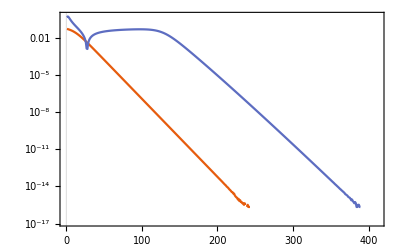

1.

1.

```mathematica
ListLogPlot[Table[Abs[{μA[k]-μA[nmax],μB[k]-μB[nmax]}],{k,0,nmax-1}]ᵀ,Joined->True,PlotRange->Full,PlotTheme->"Scientific"]
μA[nmax]
μB[nmax]
```

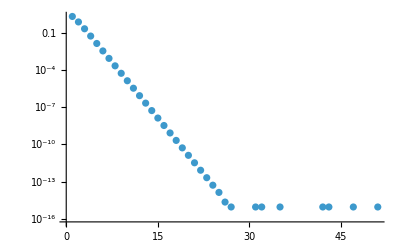

-3.

```mathematica
h=1;μ=1;
{bA,μA}=powerIteration[H2-μ*IdentityMatrix[4],Normalize[RandomReal[{-1,1},4]],nmax=1000];
ListLogPlot[Table[Abs[Min[Evaluate@vals//N]-μA[k]-μ],{k,nmax}]]
μA[nmax]+μ
```

### TFIM -- bigger systems

```mathematica
Clear[S,Ss]
Table[S[i] = SparseArray[0.5*PauliMatrix[i]],{i,0,3}];
S[4] = SparseArray[0.5*(PauliMatrix[1]+ⅈ PauliMatrix[2])];
S[5] = SparseArray[0.5*(PauliMatrix[1]-ⅈ PauliMatrix[2])];
Clear[Ss,IDL,IDR,Ns]
generateSpinMatrices[Ns_]:=Module[{Ss,H,V,vals,vecs,order,IDL,IDR},
IDL[l_]:=1.0*SparseArray[IdentityMatrix[2^(l-1)]];
IDR[l_]:=1.0*SparseArray[IdentityMatrix[2^(Ns-l)]];
Table[Ss[l,j]=KroneckerProduct[IDL[l],S[j],IDR[l]],{j,0,5},{l,Ns}];
Ss
]

Clear[powerIterationFast,A,b0,n]
powerIterationFast[A_,b0_,n_:2,tol_:10^-10]:=Module[{bk,μ,k,abk,norm,nsteps,pbk},
bk=b0;
nsteps=-1;
Do[
nsteps+=1;
abk=A.bk;
norm=bk*.bk;
μ[k]=bk*.abk/norm;
pbk=bk;
bk=abk/Norm[abk];
If[Norm[bk-Sign[μ[k]]pbk]<tol, (*Print["Finished after "<>ToString[nsteps]<>" steps."];*) Break[];];

,{k,0,n}];
{bk,μ,nsteps}]
Ss = generateSpinMatrices[nsites=12]
```

Ss$297130

```mathematica
Table[Ss[l,i].Ss[l,j]-Ss[l,j].Ss[l,i]==Sum[Signature[{i,j,k}]*ⅈ*Ss[l,k],{k,3}],{l,1},{i,3},{j,3}]
```

{{{True,True,True},{True,True,True},{True,True,True}}}

```mathematica
nsites=10;
Ss = generateSpinMatrices[nsites];
zz=Sum[Ss[l,3].Ss[l+1,3],{l,nsites-1}];
tf=Sum[Ss[l,1],{l,nsites}];
Clear[h,HN];
HN[h_]:=-4.0zz -2.0 h tf-0Sum[Ss[l,3],{l,nsites}];
```

```mathematica
Eigenvalues[HN[.1]//N]//Sort
```

Eigenvalues::arh: Because finding 1024 out of the 1024 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

{-9.03002,-9.03002,-7.21894,-7.21894,-7.18724,-7.18724,-7.13916,-7.13916,-7.0806,-7.0806,-7.01807,-7.01807,-6.95778,-6.95778,-6.90514,-6.90514,-6.86444,-6.86444,-6.83878,-6.83878,-5.37616,-5.37616,-5.32808,-5.32808,-5.29638,-5.29638,-5.26952,-5.26952,-5.23782,-5.23782,-5.20699,-5.20699,-5.18973,-5.18973,-5.17529,-5.17529,-5.1467,-5.1467,-5.1272,-5.1272,-5.11501,-5.11501,-5.09406,-5.09406,-5.06864,-5.06864,-5.06692,-5.06692,-5.06236,-5.06236,-5.05336,-5.05336,-5.0277,-5.0277,-5.02166,-5.02166,-5.01428,-5.01428,-5.00836,-5.00836,-4.996,-4.996,-4.97358,-4.97358,-4.95572,-4.95572,-4.94792,-4.94792,-4.94583,-4.94583,-4.91502,-4.91502,-4.89319,-4.89319,-4.88936,-4.88936,-4.85249,-4.85249,-4.8329,-4.8329,-4.82683,-4.82683,-4.7922,-4.7922,-4.76654,-4.76654,-4.73956,-4.73956,-4.7139,-4.7139,-4.6732,-4.6732,-3.4853,-3.4853,-3.42674,-3.42674,-3.37865,-3.37865,-3.36421,-3.36421,-3.34696,-3.34696,-3.31612,-3.31612,-3.30393,-3.30393,-3.28442,-3.28442,-3.25756,-3.25756,-3.25584,-3.25584,-3.25128,-3.25128,-3.22586,-3.22586,-3.22414,-3.22414,-3.21058,-3.21058,-3.2032,-3.2032,-3.19728,-3.19728,-3.18492,-3.18492,-3.17778,-3.17778,-3.1715,-3.1715,-3.16558,-3.16558,-3.1625,-3.1625,-3.14464,-3.14464,-3.13684,-3.13684,-3.13475,-3.13475,-3.1308,-3.1308,-3.11749,-3.11749,-3.11294,-3.11294,-3.10514,-3.10514,-3.10394,-3.10394,-3.10305,-3.10305,-3.0821,-3.0821,-3.07828,-3.07828,-3.07224,-3.07224,-3.06485,-3.06485,-3.05496,-3.05496,-3.05041,-3.05041,-3.04658,-3.04658,-3.04141,-3.04141,-3.02415,-3.02415,-3.02182,-3.02182,-3.01575,-3.01575,-3.00971,-3.00971,-3.00232,-3.00232,-2.99849,-2.99849,-2.9964,-2.9964,-2.99012,-2.99012,-2.98405,-2.98405,-2.98112,-2.98112,-2.96162,-2.96162,-2.95546,-2.95546,-2.94942,-2.94942,-2.94376,-2.94376,-2.94204,-2.94204,-2.93596,-2.93596,-2.92848,-2.92848,-2.92377,-2.92377,-2.90306,-2.90306,-2.90282,-2.90282,-2.90134,-2.90134,-2.89678,-2.89678,-2.88348,-2.88348,-2.8774,-2.8774,-2.87568,-2.87568,-2.87112,-2.87112,-2.86212,-2.86212,-2.8487,-2.8487,-2.84278,-2.84278,-2.83042,-2.83042,-2.82304,-2.82304,-2.82095,-2.82095,-2.81712,-2.81712,-2.79014,-2.79014,-2.78234,-2.78234,-2.78025,-2.78025,-2.76448,-2.76448,-2.75459,-2.75459,-2.7276,-2.7276,-2.72378,-2.72378,-2.70194,-2.70194,-2.66732,-2.66732,-2.66125,-2.66125,-2.64166,-2.64166,-2.60096,-2.60096,-2.54832,-2.54832,-1.53587,-1.53587,-1.47334,-1.47334,-1.41478,-1.41478,-1.41306,-1.41306,-1.3667,-1.3667,-1.36042,-1.36042,-1.3545,-1.3545,-1.335,-1.335,-1.31972,-1.31972,-1.30641,-1.30641,-1.30186,-1.30186,-1.29406,-1.29406,-1.29197,-1.29197,-1.27472,-1.27472,-1.26116,-1.26116,-1.25377,-1.25377,-1.24388,-1.24388,-1.23933,-1.23933,-1.2355,-1.2355,-1.22207,-1.22207,-1.21307,-1.21307,-1.21219,-1.21219,-1.19863,-1.19863,-1.19124,-1.19124,-1.18741,-1.18741,-1.18532,-1.18532,-1.18137,-1.18137,-1.17904,-1.17904,-1.17297,-1.17297,-1.15954,-1.15954,-1.15572,-1.15572,-1.15362,-1.15362,-1.15054,-1.15054,-1.13834,-1.13834,-1.13268,-1.13268,-1.13096,-1.13096,-1.12488,-1.12488,-1.11884,-1.11884,-1.11268,-1.11268,-1.10554,-1.10554,-1.10098,-1.10098,-1.09926,-1.09926,-1.09318,-1.09318,-1.09198,-1.09198,-1.09026,-1.09026,-1.0857,-1.0857,-1.0724,-1.0724,-1.06632,-1.06632,-1.0646,-1.0646,-1.06028,-1.06028,-1.06004,-1.06004,-1.05856,-1.05856,-1.0529,-1.0529,-1.0407,-1.0407,-1.03762,-1.03762,-1.03462,-1.03462,-1.0329,-1.0329,-1.0317,-1.0317,-1.01934,-1.01934,-1.0122,-1.0122,-1.01196,-1.01196,-1.00987,-1.00987,-1.00604,-1.00604,-1.00592,-1.00592,-1.,-1.,-0.992612,-0.992612,-0.986537,-0.986537,-0.980259,-0.980259,-0.979055,-0.979055,-0.978169,-0.978169,-0.97434,-0.97434,-0.971256,-0.971256,-0.969166,-0.969166,-0.953395,-0.953395,-0.951913,-0.951913,-0.947358,-0.947358,-0.943507,-0.943507,-0.939559,-0.939559,-0.937469,-0.937469,-0.930081,-0.930081,-0.926253,-0.926253,-0.921698,-0.921698,-0.916524,-0.916524,-0.912696,-0.912696,-0.91181,-0.91181,-0.899271,-0.899271,-0.890865,-0.890865,-0.889382,-0.889382,-0.884827,-0.884827,-0.880999,-0.880999,-0.873611,-0.873611,-0.871521,-0.871521,-0.863722,-0.863722,-0.859168,-0.859168,-0.856241,-0.856241,-0.850165,-0.850165,-0.83674,-0.83674,-0.832912,-0.832912,-0.830822,-0.830822,-0.830581,-0.830581,-0.824544,-0.824544,-0.818468,-0.818468,-0.81108,-0.81108,-0.805162,-0.805162,-0.798884,-0.798884,-0.789882,-0.789882,-0.77818,-0.77818,-0.776456,-0.776456,-0.770381,-0.770381,-0.758185,-0.758185,-0.75252,-0.75252,-0.750797,-0.750797,-0.73724,-0.73724,-0.717896,-0.717896,-0.711821,-0.711821,-0.710097,-0.710097,-0.705543,-0.705543,-0.692236,-0.692236,-0.657455,-0.657455,-0.655365,-0.655365,-0.651537,-0.651537,-0.629706,-0.629706,-0.598895,-0.598895,-0.589006,-0.589006,-0.536364,-0.536364,-0.476081,-0.476081,0.476081,0.476081,0.536364,0.536364,0.589006,0.589006,0.598895,0.598895,0.629706,0.629706,0.651537,0.651537,0.655365,0.655365,0.657455,0.657455,0.692236,0.692236,0.705543,0.705543,0.710097,0.710097,0.711821,0.711821,0.717896,0.717896,0.73724,0.73724,0.750797,0.750797,0.75252,0.75252,0.758185,0.758185,0.770381,0.770381,0.776456,0.776456,0.77818,0.77818,0.789882,0.789882,0.798884,0.798884,0.805162,0.805162,0.81108,0.81108,0.818468,0.818468,0.824544,0.824544,0.830581,0.830581,0.830822,0.830822,0.832912,0.832912,0.83674,0.83674,0.850165,0.850165,0.856241,0.856241,0.859168,0.859168,0.863722,0.863722,0.871521,0.871521,0.873611,0.873611,0.880999,0.880999,0.884827,0.884827,0.889382,0.889382,0.890865,0.890865,0.899271,0.899271,0.91181,0.91181,0.912696,0.912696,0.916524,0.916524,0.921698,0.921698,0.926253,0.926253,0.930081,0.930081,0.937469,0.937469,0.939559,0.939559,0.943507,0.943507,0.947358,0.947358,0.951913,0.951913,0.953395,0.953395,0.969166,0.969166,0.971256,0.971256,0.97434,0.97434,0.978169,0.978169,0.979055,0.979055,0.980259,0.980259,0.986537,0.986537,0.992612,0.992612,1.,1.,1.00592,1.00592,1.00604,1.00604,1.00987,1.00987,1.01196,1.01196,1.0122,1.0122,1.01934,1.01934,1.0317,1.0317,1.0329,1.0329,1.03462,1.03462,1.03762,1.03762,1.0407,1.0407,1.0529,1.0529,1.05856,1.05856,1.06004,1.06004,1.06028,1.06028,1.0646,1.0646,1.06632,1.06632,1.0724,1.0724,1.0857,1.0857,1.09026,1.09026,1.09198,1.09198,1.09318,1.09318,1.09926,1.09926,1.10098,1.10098,1.10554,1.10554,1.11268,1.11268,1.11884,1.11884,1.12488,1.12488,1.13096,1.13096,1.13268,1.13268,1.13834,1.13834,1.15054,1.15054,1.15362,1.15362,1.15572,1.15572,1.15954,1.15954,1.17297,1.17297,1.17904,1.17904,1.18137,1.18137,1.18532,1.18532,1.18741,1.18741,1.19124,1.19124,1.19863,1.19863,1.21219,1.21219,1.21307,1.21307,1.22207,1.22207,1.2355,1.2355,1.23933,1.23933,1.24388,1.24388,1.25377,1.25377,1.26116,1.26116,1.27472,1.27472,1.29197,1.29197,1.29406,1.29406,1.30186,1.30186,1.30641,1.30641,1.31972,1.31972,1.335,1.335,1.3545,1.3545,1.36042,1.36042,1.3667,1.3667,1.41306,1.41306,1.41478,1.41478,1.47334,1.47334,1.53587,1.53587,2.54832,2.54832,2.60096,2.60096,2.64166,2.64166,2.66125,2.66125,2.66732,2.66732,2.70194,2.70194,2.72378,2.72378,2.7276,2.7276,2.75459,2.75459,2.76448,2.76448,2.78025,2.78025,2.78234,2.78234,2.79014,2.79014,2.81712,2.81712,2.82095,2.82095,2.82304,2.82304,2.83042,2.83042,2.84278,2.84278,2.8487,2.8487,2.86212,2.86212,2.87112,2.87112,2.87568,2.87568,2.8774,2.8774,2.88348,2.88348,2.89678,2.89678,2.90134,2.90134,2.90282,2.90282,2.90306,2.90306,2.92377,2.92377,2.92848,2.92848,2.93596,2.93596,2.94204,2.94204,2.94376,2.94376,2.94942,2.94942,2.95546,2.95546,2.96162,2.96162,2.98112,2.98112,2.98405,2.98405,2.99012,2.99012,2.9964,2.9964,2.99849,2.99849,3.00232,3.00232,3.00971,3.00971,3.01575,3.01575,3.02182,3.02182,3.02415,3.02415,3.04141,3.04141,3.04658,3.04658,3.05041,3.05041,3.05496,3.05496,3.06485,3.06485,3.07224,3.07224,3.07828,3.07828,3.0821,3.0821,3.10305,3.10305,3.10394,3.10394,3.10514,3.10514,3.11294,3.11294,3.11749,3.11749,3.1308,3.1308,3.13475,3.13475,3.13684,3.13684,3.14464,3.14464,3.1625,3.1625,3.16558,3.16558,3.1715,3.1715,3.17778,3.17778,3.18492,3.18492,3.19728,3.19728,3.2032,3.2032,3.21058,3.21058,3.22414,3.22414,3.22586,3.22586,3.25128,3.25128,3.25584,3.25584,3.25756,3.25756,3.28442,3.28442,3.30393,3.30393,3.31612,3.31612,3.34696,3.34696,3.36421,3.36421,3.37865,3.37865,3.42674,3.42674,3.4853,3.4853,4.6732,4.6732,4.7139,4.7139,4.73956,4.73956,4.76654,4.76654,4.7922,4.7922,4.82683,4.82683,4.8329,4.8329,4.85249,4.85249,4.88936,4.88936,4.89319,4.89319,4.91502,4.91502,4.94583,4.94583,4.94792,4.94792,4.95572,4.95572,4.97358,4.97358,4.996,4.996,5.00836,5.00836,5.01428,5.01428,5.02166,5.02166,5.0277,5.0277,5.05336,5.05336,5.06236,5.06236,5.06692,5.06692,5.06864,5.06864,5.09406,5.09406,5.11501,5.11501,5.1272,5.1272,5.1467,5.1467,5.17529,5.17529,5.18973,5.18973,5.20699,5.20699,5.23782,5.23782,5.26952,5.26952,5.29638,5.29638,5.32808,5.32808,5.37616,5.37616,6.83878,6.83878,6.86444,6.86444,6.90514,6.90514,6.95778,6.95778,7.01807,7.01807,7.0806,7.0806,7.13916,7.13916,7.18724,7.18724,7.21894,7.21894,9.03002,9.03002}

```mathematica
ns=Table[n,{n,2,18}];
Monitor[
Clear[h,v,nm,ene,mag,corr];
Do[
Ss = generateSpinMatrices[nsites];
zz=Sum[Ss[l,3].Ss[l+1,3],{l,nsites-1}];
tf=Sum[Ss[l,1],{l,nsites}];
Clear[h,HN];
HN[h_]:=-4.0zz -2.0 h tf-10^-2 Sum[Ss[l,3],{l,nsites}];
hs = Table[h,{h,$MachineEpsilon,2,0.01}];
step=0;
Do[
μ=1;
HNm=HN[h];
AbsoluteTiming[{bA,μA,nmax}=powerIterationFast[HNm-μ*IdentityMatrix[2^nsites],Table[1,Length[HNm]],10000,10^-4];];
ListLogPlot[Table[Abs[μA[nmax]-μA[k]],{k,nmax}]];
ene[nsites,step]=bA*.HNm.bA;
Table[mag[nsites,step,s]=1/nsites Sum[bA*.Ss[l,s].bA,{l,nsites}],{s,3}];
(*v[nsites,step]=bA;*)
nm[nsites,step]=nmax;
step+=1;
,{h,hs}];
,{nsites,ns}];,{h,nsites}];
```

$Aborted

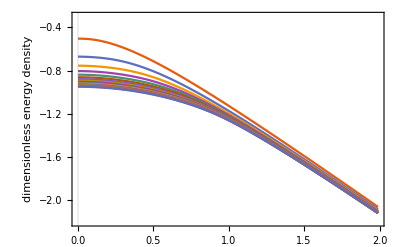

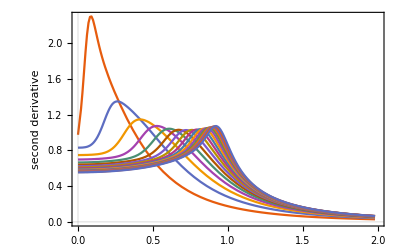

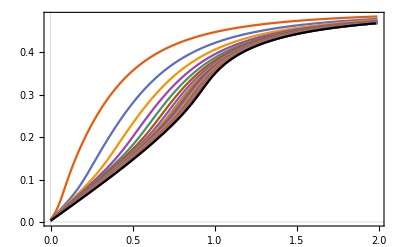

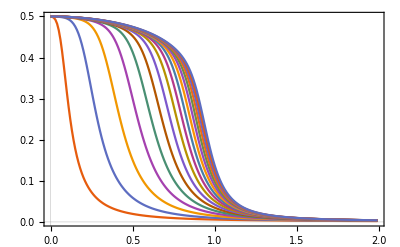

```mathematica
ListPlot[edata=Table[{hs[[nh]],ene[nsites,nh]/nsites},{nh,step},{nsites,ns}]ᵀ,Joined->True,PlotRange->{-2.2,-0.3},PlotTheme->"Scientific",FrameLabel->{"","dimensionless energy density "}]
fs=Interpolation[#]&/@edata;
Plot[Evaluate@Table[-fs[[nsites]]''[x],{nsites,Length[ns]}],{x,0,2},PlotTheme->"Scientific",FrameLabel->{"","second derivative "}]

ListPlot[Table[{hs[[nh]],mag[nsites,nh,1]},{nh,step},{nsites,ns}]ᵀ,Joined->True,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"",""}];
Show[%,Plot[-0.5*fs[[-1]]'[x],{x,0,2},PlotTheme->"Scientific",PlotStyle->Black]]

ListPlot[magdata=Table[{hs[[nh]],mag[nsites,nh,3]},{nh,step},{nsites,ns}]ᵀ,Joined->True,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"",""}]
```

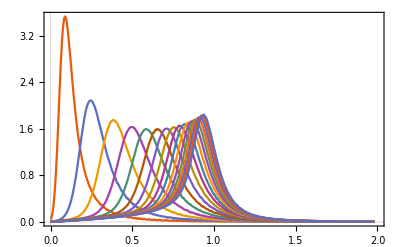

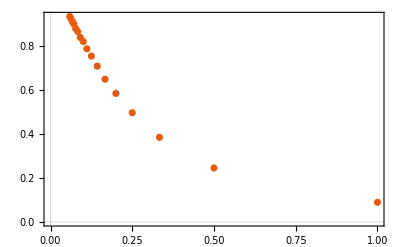

FittedModel[…]

1.06189-2.36556 x

1.06189

```mathematica
fs=Interpolation[#]&/@magdata;
Plot[Evaluate@Table[-fs[[nsites]]'[x],{nsites,Length[ns]}],{x,0,2},PlotRange->Full,PlotTheme->"Scientific"]

ListPlot[maxpos=Table[{1/nsites,x/.FindMaximum[-fs[[nsites]]'[x],{x,0,2}][[2]]},{nsites,Length[ns]}],PlotTheme->"Scientific"]
f=LinearModelFit[maxpos[[4;;]],x,x]
Normal[f]
f[0]
```

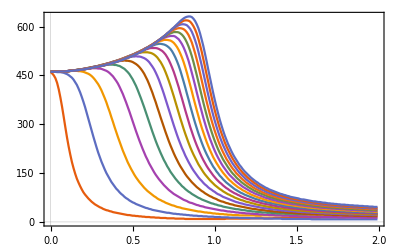

```mathematica
ListPlot[Table[{hs[[nh]],nm[nsites,nh]},{nh,step},{nsites,ns}]ᵀ,Joined->True,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"",""}]
```

### Heisenberg -- bigger systems

```mathematica
Clear[S,Ss]
Table[S[i] = SparseArray[0.5*PauliMatrix[i]],{i,0,3}];
S[4] = SparseArray[0.5*(PauliMatrix[1]+ⅈ PauliMatrix[2])];
S[5] = SparseArray[0.5*(PauliMatrix[1]-ⅈ PauliMatrix[2])];
Clear[Ss,IDL,IDR,Ns]
generateSpinMatrices[Ns_]:=Module[{Ss,H,V,vals,vecs,order,IDL,IDR},
IDL[l_]:=1.0*SparseArray[IdentityMatrix[2^(l-1)]];
IDR[l_]:=1.0*SparseArray[IdentityMatrix[2^(Ns-l)]];
Table[Ss[l,j]=KroneckerProduct[IDL[l],S[j],IDR[l]],{j,0,5},{l,Ns}];
Ss
]

Clear[powerIterationFast,A,b0,n]
powerIterationFast[A_,b0_,n_:2,tol_:10^-10]:=Module[{bk,μ,k,abk,norm,nsteps,pbk},
bk=b0;
nsteps=-1;
Do[
nsteps+=1;
abk=A.bk;
norm=bk*.bk;
μ[k]=bk*.abk/norm;
pbk=bk;
bk=abk/Norm[abk];
If[Norm[bk-Sign[μ[k]]pbk]<tol, (*Print["Finished after "<>ToString[nsteps]<>" steps."];*) Break[];];

,{k,0,n}];
{bk,μ,nsteps}]
Ss = generateSpinMatrices[nsites=12]
```

Ss$19857

```mathematica
Table[Ss[l,i].Ss[l,j]-Ss[l,j].Ss[l,i]==Sum[Signature[{i,j,k}]*ⅈ*Ss[l,k],{k,3}],{l,1},{i,3},{j,3}]
```

{{{True,True,True},{True,True,True},{True,True,True}}}

```mathematica
ns=Table[n,{n,7,14}];
Monitor[
Clear[h,v,nm,ene,mag,corr];
Do[
Ss = generateSpinMatrices[nsites];
xx=Sum[Ss[l,1].Ss[l+1,1],{l,nsites-1}];
yy=Sum[Ss[l,2].Ss[l+1,2],{l,nsites-1}];
zz=Sum[Ss[l,3].Ss[l+1,3],{l,nsites-1}];
tf=Sum[Ss[l,1],{l,nsites}];
Clear[h,HN];
HN[h_]:=4.0xx+4.0yy+4.0zz -2.0 h tf-10^-2 Sum[Ss[l,3],{l,nsites}];
hs = Table[h,{h,$MachineEpsilon,2,0.01}];
step=0;
Do[
μ=1;
HNm=HN[h];
AbsoluteTiming[{bA,μA,nmax}=powerIterationFast[HNm-μ*IdentityMatrix[2^nsites],Table[1,Length[HNm]],10000,10^-4];];
ListLogPlot[Table[Abs[μA[nmax]-μA[k]],{k,nmax}]];
ene[nsites,step]=bA*.HNm.bA;
Table[mag[nsites,step,s]=1/nsites Sum[bA*.Ss[l,s].bA,{l,nsites}],{s,3}];
(*v[nsites,step]=bA;*)
nm[nsites,step]=nmax;
step+=1;
,{h,hs}];
,{nsites,ns}];,{h,nsites}];
```

$Aborted

```mathematica
ListPlot[edata=Table[{hs[[nh]],ene[nsites,nh]/nsites},{nh,step},{nsites,ns}]ᵀ,Joined->True,PlotRange->{-2.2,-0.8},PlotTheme->"Scientific",FrameLabel->{"","dimensionless energy density "}]
fs=Interpolation[#]&/@edata;
Plot[Evaluate@Table[-fs[[nsites]]''[x],{nsites,Length[ns]}],{x,0,2},PlotTheme->"Scientific",FrameLabel->{"","second derivative "}]

ListPlot[Table[{hs[[nh]],mag[nsites,nh,1]},{nh,step},{nsites,ns}]ᵀ,Joined->True,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"",""}];
Show[%,Plot[-0.5*fs[[-1]]'[x],{x,0,2},PlotTheme->"Scientific",PlotStyle->Black]]

ListPlot[magdata=Table[{hs[[nh]],mag[nsites,nh,3]},{nh,step},{nsites,ns}]ᵀ,Joined->True,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"",""}]
```

```mathematica
fs=Interpolation[#]&/@magdata;
Plot[Evaluate@Table[-fs[[nsites]]'[x],{nsites,Length[ns]}],{x,0,2},PlotRange->Full,PlotTheme->"Scientific"]

ListPlot[maxpos=Table[{1/nsites,x/.FindMaximum[-fs[[nsites]]'[x],{x,0,2}][[2]]},{nsites,Length[ns]}],PlotTheme->"Scientific"]
f=LinearModelFit[maxpos[[4;;]],x,x]
Normal[f]
f[0]
```

```mathematica
ListPlot[Table[{hs[[nh]],nm[nsites,nh]},{nh,step},{nsites,ns}]ᵀ,Joined->True,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"",""}]
```